# 3 body Hamiltonian

#### Definitions

```mathematica
Clear[b]
```

```mathematica
αβγ[b_]:={-((b[[1]]+b[[2]])/4+b[[3]]),-(b[[1]]+b[[2]]),(b[[1]]-b[[2]])/2}
```

```mathematica
Expand[α β-γ^2/.{α->-((b1+b2)/4+b3),β->-(b1+b2),γ->(b1-b2)/2}]
```

b1 b2+b1 b3+b2 b3

```mathematica
pow=1;
```

```mathematica
Solve[{α==-((b1+b2)/4+b3),β==-(b1+b2),γ==(b1-b2)/2},{b1,b2,b3}]
```

{{b1→1/2 (-β+2 γ),b2→1/2 (-β-2 γ),b3→-α+β/4}}

```mathematica
int[α_]:=(√(2/π)NIntegrate[r^2 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞}])
```

```mathematica
intp[α_]:=(√(2/π)α^(3/2) NIntegrate[r^2 Exp[-α r^2/2]/Cosh[r^pow],{r,0,∞}])
```

Check this integral for α very large (should be one)

```mathematica
int[99999999]
```

1.

```mathematica
Clear[α]
```

```mathematica
as=AsymptoticIntegrate[√(2/π)r^2 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞},{α,∞,30}];
```

```mathematica
ass=PadeApproximant[as,{α,∞,{14,15}}];
```

```mathematica
ass=N[ass]
```

(1.+(2.28903×10^10)/α^14+(2.55033×10^12)/α^13+(7.27493×10^12)/α^12+(8.08866×10^12)/α^11+(4.74551×10^12)/α^10+(1.67237×10^12)/α^9+(3.79697×10^11)/α^8+(5.78329×10^10)/α^7+(6.04099×10^9)/α^6+(4.36137×10^8)/α^5+(2.16338×10^7)/α^4+720572./α^3+15332.9/α^2+187.58/α)/(1.+(1.41453×10^11)/α^15+(3.10256×10^12)/α^14+(1.14729×10^13)/α^13+(1.76328×10^13)/α^12+(1.43999×10^13)/α^11+(7.03691×10^12)/α^10+(2.20465×10^12)/α^9+(4.62202×10^11)/α^8+(6.65676×10^10)/α^7+(6.67818×10^9)/α^6+(4.67999×10^8)/α^5+(2.27018×10^7)/α^4+743410./α^3+15613.4/α^2+189.08/α)

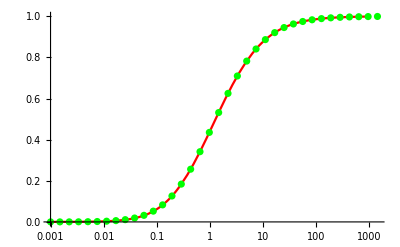

```mathematica
Block[{α},Show[{LogLinearPlot[N[ass],{α,0.001,1000}, PlotStyle->Red],ListLogLinearPlot[Table[{α=0.001 1.5^i,int[α]},{i,0,35}],PlotStyle->Green]},PlotRange->All]]
```

```mathematica
int[α_]=ass
```

(1.+(2.28903×10^10)/α^14+(2.55033×10^12)/α^13+(7.27493×10^12)/α^12+(8.08866×10^12)/α^11+(4.74551×10^12)/α^10+(1.67237×10^12)/α^9+(3.79697×10^11)/α^8+(5.78329×10^10)/α^7+(6.04099×10^9)/α^6+(4.36137×10^8)/α^5+(2.16338×10^7)/α^4+720572./α^3+15332.9/α^2+187.58/α)/(1.+(1.41453×10^11)/α^15+(3.10256×10^12)/α^14+(1.14729×10^13)/α^13+(1.76328×10^13)/α^12+(1.43999×10^13)/α^11+(7.03691×10^12)/α^10+(2.20465×10^12)/α^9+(4.62202×10^11)/α^8+(6.65676×10^10)/α^7+(6.67818×10^9)/α^6+(4.67999×10^8)/α^5+(2.27018×10^7)/α^4+743410./α^3+15613.4/α^2+189.08/α)

```mathematica
int2[α_]:=(1/3/√(π/2)NIntegrate[r^4 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞}])
```

```mathematica
as2=AsymptoticIntegrate[1/3/√(π/2)r^4 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞},{α,∞,30}];
```

```mathematica
ass2=PadeApproximant[as2,{α,∞,{14,15}}];
```

```mathematica
ass2=N[ass2]
```

(1.-(1.64435×10^11)/α^14+(9.33855×10^12)/α^13+(2.29001×10^13)/α^12+(2.19496×10^13)/α^11+(1.12652×10^13)/α^10+(3.5188×10^12)/α^9+(7.1591×10^11)/α^8+(9.86128×10^10)/α^7+(9.3882×10^9)/α^6+(6.21908×10^8)/α^5+(2.84712×10^7)/α^4+879744./α^3+17445.9/α^2+199.721/α)/(1.+(3.54648×10^12)/α^15+(2.78821×10^13)/α^14+(6.64773×10^13)/α^13+(7.55456×10^13)/α^12+(4.8822×10^13)/α^11+(1.96967×10^13)/α^10+(5.24638×10^12)/α^9+(9.55589×10^11)/α^8+(1.21579×10^11)/α^7+(1.0918×10^10)/α^6+(6.92266×10^8)/α^5+(3.06535×10^7)/α^4+923157./α^3+17944.2/α^2+202.221/α)

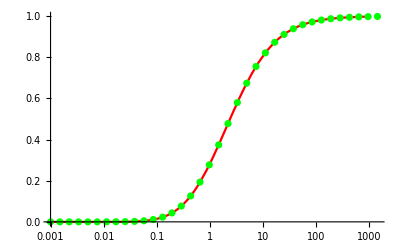

```mathematica
Block[{α},Show[{LogLinearPlot[N[ass2],{α,0.001,1000}, PlotStyle->Red],ListLogLinearPlot[Table[{α=0.001 1.5^i,int2[α]},{i,0,35}],PlotStyle->Green]},PlotRange->All]]
```

```mathematica
int2[α_]=ass2
```

(1.-(1.64435×10^11)/α^14+(9.33855×10^12)/α^13+(2.29001×10^13)/α^12+(2.19496×10^13)/α^11+(1.12652×10^13)/α^10+(3.5188×10^12)/α^9+(7.1591×10^11)/α^8+(9.86128×10^10)/α^7+(9.3882×10^9)/α^6+(6.21908×10^8)/α^5+(2.84712×10^7)/α^4+879744./α^3+17445.9/α^2+199.721/α)/(1.+(3.54648×10^12)/α^15+(2.78821×10^13)/α^14+(6.64773×10^13)/α^13+(7.55456×10^13)/α^12+(4.8822×10^13)/α^11+(1.96967×10^13)/α^10+(5.24638×10^12)/α^9+(9.55589×10^11)/α^8+(1.21579×10^11)/α^7+(1.0918×10^10)/α^6+(6.92266×10^8)/α^5+(3.06535×10^7)/α^4+923157./α^3+17944.2/α^2+202.221/α)

```mathematica
detb[b_]:=b[[1]] b[[2]]+b[[2]] b[[3]]+b[[3]]b[[1]]
```

```mathematica
dαβγ[α_,β_,γ_]:=α β -γ^2
```

```mathematica
Clear[matrixel];matrixel[b_,bp_,λ0_:1.3,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,ovl,kin,pot, s,arg},
arg[bs_]:=-(bs⟦2⟧ bs⟦3⟧+bs⟦1⟧ (bs⟦2⟧+bs⟦3⟧))/(bs[[1]]+bs[[2]]);
bs=b+bp;
{α,β,γ}=αβγ[b];{αp,βp,γp}=αβγ[bp]; {αs,βs,γs}=αβγ[bs];
s={-λ0(λ0-1)/2,-λ0(λ0+1)/2,-λ0(λ0+1)/2};
ovl=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2);
kin=
3/4(3β βp αs+4 α αp βs-4(α γp^2+αp γ^2)-3(β γp^2+βp γ^2))/dαβγ[αs,βs,γs] ovl;
If[debug,Return[{ovl,kin,ovl int[arg[bs]],ovl  int[arg[RotateLeft[bs,1]]],ovl int[arg[RotateLeft[bs,2]]]}],
pot=ovl(Plus@@{s[[1]] int[arg[bs]],s[[2]] int[arg[RotateLeft[bs,1]]],s[[3]] int[arg[RotateLeft[bs,2]]]});
{ovl,kin+pot}]
]
```

```mathematica
Clear[ovlel];ovlel[b_,bp_,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,ovl,kin,pot, s,arg},
arg[bs_]:=-(bs⟦2⟧ bs⟦3⟧+bs⟦1⟧ (bs⟦2⟧+bs⟦3⟧))/(bs[[1]]+bs[[2]]);
bs=b+bp;
{α,β,γ}=αβγ[b];{αp,βp,γp}=αβγ[bp]; {αs,βs,γs}=αβγ[bs];
ovl=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)
]
```

### L = 1

```mathematica
dαβγc[α_,β_,γ_,cmm_,cpp_,cmp_]:=(*If[γ==0.,(cmm β+cpp α-cmp 10^-9)/(α β),*)(cmm β+cpp α-cmp γ)/(α β-γ^2) (*]*)
```

```mathematica
?dαβγ
```

```mathematica
Clear[ctopm];ctopm[c_]:={c[[3]],(c[[2]]-c[[1]])/2}
```

```mathematica
Table[RotateLeft[{b1,b2,b3},i-1],{i,3}]
```

{{b1,b2,b3},{b2,b3,b1},{b3,b1,b2}}

```mathematica
Simplify[αβγ/@Table[RotateLeft[{b,b,x},i-1],{i,3}]]
```

{{-b/2-x,-2 b,0},{1/4 (-5 b-x),-b-x,(b-x)/2},{1/4 (-5 b-x),-b-x,1/2 (-b+x)}}

```mathematica
Clear[matrixel1];matrixel1[bc_,bcp_,λ0_:1.3,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,cp,cm,cpp,cpm,ovl,ovl0,kin,pot, s,v2},
bs=bc[[1]]+bcp[[1]];
{α,β,γ}=αβγ[bc[[1]]];{αp,βp,γp}=αβγ[bcp[[1]]]; {αs,βs,γs}=αβγ[bs];
{cp,cm}=ctopm[bc[[2]]];{cpp,cpm}=ctopm[bcp[[2]]];
s={-λ0(λ0-1)/2,-λ0(λ0+1)/2,-λ0(λ0+1)/2};
v2[bs_,c1i_,c2i_]:=Block[{cpi,cmi,cppi,cpmi,αsi,βsi,γsi,ϵ,δ},{αsi,βsi,γsi}=αβγ[bs];{cpi,cmi}=ctopm[c1i];{cppi,cpmi}=ctopm[c2i];δ=αsi-γsi^2/βsi;ϵ=(cmi βsi-cpi γsi)(cpmi βsi-cppi γsi)/βsi;(*Print[{c1i,c2i,αsi,βsi,γsi,δ,ϵ, cpi cppi, int[δ],int2[δ]}];*)(*(cpi cppi δ int[δ]+ ϵ int2[δ])/(cpi cppi δ +ϵ)*)(cpi cppi δ int[δ]+ ϵ int2[δ])/dαβγ[αsi,βsi,γsi]];

ovl0=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)/(dαβγc[2α,2β,2γ,cm cm,cp cp,2cm cp]^(1/2)dαβγc[2αp,2βp,2γp,cpm cpm,cpp cpp,2cpm cpp]^(1/2));
ovl=ovl0
dαβγc[α+αp,β+βp,γ+γp,cm cpm,cp cpp,cpm cp+cm cpp];
kin=
(cm cpp (8 αp^2 (β+βp) γ+3 (γ+γp) (3 βp γ^2+β γp (-2 γ+γp))+(α+αp) (6 β^2 γp-3 β βp (3 γ+γp))+4 (γ+γp) (αp γ (γ-2 γp)+3 α γp^2)-4α αp (β+βp) (γ+3 γp))+cm cpm (-3 βp (β+3 βp) γ^2-3 β (3 β+βp) γp^2+12 γ  β βp γp+8 γ γp (γ+γp)^2+3 (α+αp)(β+βp) β βp-12 (β+βp) ( αp γ^2+ α γp^2)-8 (α+αp) (β+βp)γ γp  +12α αp(β+βp)^2)+cp cpp (-3(α+αp) (3 βp γ^2+2 (β+βp) γ γp+3 β γp^2)+9(α+αp)^2 ( β βp)-12( γ^2 αp^2+α^2 γp^2)+4α αp(α+αp) (β+βp)+6 γ γp (γ+γp)^2-4α  αp (γ^2-4 γ γp+γp^2))+cp cpm (-α βp(-6 βp γ)-α βp(3 β (γ+3 γp))+3αp βp (2 βp γ-β (γ+3 γp))+4 (γ+γp) (3 αp γ^2+α γp (-2 γ+γp))+8 α^2 (β+βp) γp-4α  αp (β+βp) (3 γ+γp)+3 (γ+γp) (βp γ (γ-2 γp)+3 β γp^2)))/(4 ((α +αp) (β+βp)-(γ+γp)^2)^2)ovl0+1/2(3β βp αs+4 α αp βs-4(α γp^2+αp γ^2)-3(β γp^2+βp γ^2))/dαβγ[αs,βs,γs] ovl;
If[debug,Print[{ovl,kin,Table[ovl0  v2[RotateLeft[bs,i-1],RotateLeft[bc[[2]],i-1],RotateLeft[bcp[[2]],i-1]],{i,3}]}],pot=ovl0(Plus@@Table[ s[[i]] v2[RotateLeft[bs,i-1],RotateLeft[bc[[2]],i-1],RotateLeft[bcp[[2]],i-1]],{i,3}]);{ovl,kin+pot}]
]
```

```mathematica
Clear[ovlel1];ovlel1[bc_,bcp_,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,cp,cm,cpp,cpm,ovl,ovl0,kin,pot, s,v2},
bs=bc[[1]]+bcp[[1]];
{α,β,γ}=αβγ[bc[[1]]];{αp,βp,γp}=αβγ[bcp[[1]]]; {αs,βs,γs}=αβγ[bs];
{cp,cm}=ctopm[bc[[2]]];{cpp,cpm}=ctopm[bcp[[2]]];
ovl0=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)/(dαβγc[2α,2β,2γ,cm cm,cp cp,2cm cp]^(1/2)dαβγc[2αp,2βp,2γp,cpm cpm,cpp cpp,2cpm cpp]^(1/2));
ovl=ovl0
dαβγc[α+αp,β+βp,γ+γp,cm cpm,cp cpp,cpm cp+cm cpp]
]
```

## Calculation

### L=0

```mathematica
bs=Block[{t},t=Table[-0.002 3.3^i, {i,5}];DeleteCases[Flatten[Outer[List,t,t,t],2],{a_,b_,c_}/;a>b]];
```

```mathematica
p12[bs_]:={bs[[2]],bs[[1]],bs[[3]]}
```

```mathematica
mm=Outer[((matrixel[#1,#2,1.5]+matrixel[#1,p12[#2],1.5])/Sqrt[(1.+ovlel[#2,p12[#2]])(1.+ovlel[#1,p12[#1]])])&,bs,bs,1];
```

```mathematica
ov=Map[#[[1]]&,mm,{2}];
```

```mathematica
ham=Map[#[[2]]&,mm,{2}];
```

```mathematica
Chop[SparseArray[ham-Transpose[ham]]]
```

SparseArray[…]

```mathematica
ham[[1,2]]
```

-0.00164164

```mathematica
ham[[2,1]]
```

-0.00164164

```mathematica
Eigenvalues[ov]
```

{37.0299,13.5583,8.22774,4.65429,2.68111,2.63653,1.47268,1.07607,0.771521,0.658123,0.445934,0.402253,0.247133,0.203502,0.185873,0.14044,0.121545,0.110998,0.0684196,0.0503936,0.0444366,0.0344053,0.030936,0.0278507,0.0179314,0.0172612,0.0146164,0.012228,0.0104238,0.00854554,0.00604624,0.00572579,0.0040874,0.003584,0.00339294,0.00263685,0.00219635,0.00191227,0.00169002,0.00121473,0.000975429,0.000941114,0.000818608,0.000600533,0.000510031,0.0004481,0.000313722,0.00026922,0.000218753,0.000208209,0.000165713,0.000141659,0.000113431,0.0000933833,0.0000621275,0.0000561796,0.0000464914,0.0000292326,0.0000269458,0.0000221251,0.0000126987,9.67641×10^-6,9.27146×10^-6,7.20815×10^-6,4.93587×10^-6,4.04285×10^-6,3.13404×10^-6,2.10694×10^-6,1.35129×10^-6,9.5237×10^-7,1.71055×10^-7,1.13142×10^-7,9.88187×10^-8,5.9113×10^-9,3.15289×10^-9}

```mathematica
evs=Sort[Eigenvalues[{ham,ov}]]
```

{-0.519835,-0.182729,-0.146256,-0.059875,0.0270131,0.0611891,0.0904237,0.112593,0.119889,0.148889,0.176054,0.205331,0.235149,0.267809,0.321275,0.348688,0.388189,0.422456,0.441372,0.482195,0.53122,0.552153,0.595878,0.646768,0.674566,0.736151,0.760639,0.787135,0.911444,0.947572,1.01979,1.12926,1.16915,1.23884,1.30198,1.38873,1.49297,1.55968,1.63489,1.63814,1.72069,1.74749,1.96819,2.06818,2.09625,2.11699,2.22876,2.25659,2.33958,2.45354,2.48795,2.5566,2.7052,2.85576,2.9398,2.96968,3.07929,3.28946,3.41636,3.55268,3.77476,4.01135,4.08866,4.43434,4.53306,4.88022,5.00087,5.28194,5.40646,6.39572,6.53053,7.10163,7.93273,8.19433,8.37364}

```mathematica
ind=Table[i,{i,Length[evs]}]-1;
```

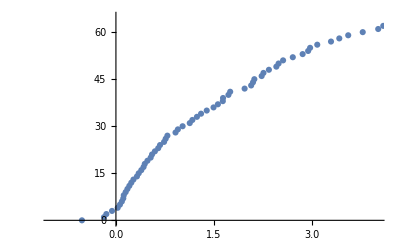

```mathematica
ListPlot[Transpose[{evs,ind}],PlotRange->{{-1,4},{-0.5,65}},PlotMarkers->Automatic]
```

```mathematica
gs=Sort[Transpose[Eigensystem[{ham,ov}]],#1[[1]]<#2[[1]]&][[1]]
```

{-0.519835,{-9.48046×10^-6,0.0000332456,-0.0000933419,0.000138366,-0.000066629,0.0000676464,-0.000225431,0.000581325,-0.000824488,0.00050553,-0.000119383,0.000362381,-0.000886001,0.00113562,-0.00103339,-0.000122457,0.000516391,-0.001448,0.00238097,0.00162744,0.00036378,-0.00178669,0.00353076,-0.00534412,-0.00043844,0.000159026,-0.000185992,-0.00471963,0.00323104,-0.00124851,0.0000893937,-0.00051286,0.00258271,-0.00840248,-0.0235242,-4.96618×10^-6,0.000340636,-0.00576903,0.0176131,0.0349812,-0.000232609,-0.0013162,-0.00270148,-0.0163828,-0.011696,0.000777155,0.00042503,-0.0081167,0.00321546,0.000108235,-0.000136574,0.000701152,-0.0012616,-0.00676369,-0.525324,0.000309004,-0.00203021,0.00372822,0.00950059,0.782194,0.00113141,-0.000343522,-0.00824365,-0.000597518,-0.295977,-0.0412246,0.066678,-0.0316754,-0.00214797,0.0422372,-0.0652813,0.0884755,-0.0236057,-0.000511817,-0.00337087}}

```mathematica
gs=gs[[2]]/Sqrt[gs[[2]].(ov.gs[[2]])]
```

{-0.000296912,0.0010412,-0.00292331,0.00433338,-0.00208671,0.00211857,-0.00706013,0.0182061,-0.0258216,0.0158324,-0.00373886,0.0113492,-0.027748,0.0355656,-0.032364,-0.00383514,0.0161725,-0.0453489,0.074568,0.0509687,0.011393,-0.0559559,0.110577,-0.167369,-0.0137312,0.00498042,-0.00582494,-0.147811,0.101191,-0.0391012,0.00279966,-0.0160619,0.0808862,-0.263151,-0.736738,-0.000155532,0.0106681,-0.180676,0.551613,1.09555,-0.00728492,-0.041221,-0.0846057,-0.51308,-0.366299,0.0243392,0.0133112,-0.254201,0.100703,0.00338973,-0.00427728,0.0219589,-0.039511,-0.211827,-16.4522,0.00967749,-0.0635827,0.116762,0.297542,24.497,0.0354338,-0.0107585,-0.258177,-0.0187132,-9.26948,-1.29108,2.08824,-0.992019,-0.0672709,1.3228,-2.0445,2.7709,-0.739291,-0.0160292,-0.10557}

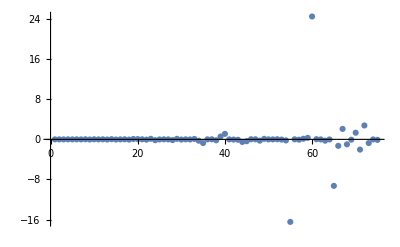

```mathematica
ListPlot[gs,PlotRange->All]
```

### L=1

```mathematica
cs={{1/2,1/2,-1},{-1,1,0}}
```

{{1/2,1/2,-1},{-1,1,0}}

```mathematica
bs1=Block[{t},t=Table[-0.002 3.3^i, {i,5}];Select[Flatten[Outer[List,t,t,t],2],#[[1]]<#[[2]]&]];
```

```mathematica
lnd=LogNormalDistribution[-1,2]
```

LogNormalDistribution[-1,2]

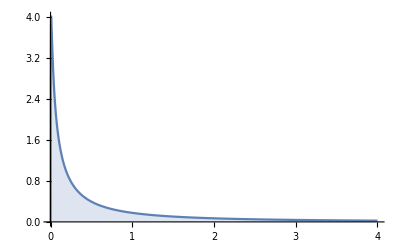

```mathematica
Plot[PDF[lnd,x]//Evaluate,{x,0,4},Filling->Axis,PlotRange->All]
```

```mathematica
p121[bcs_]:={{bcs[[1,2]],bcs[[1,1]],bcs[[1,3]]},{bcs[[2,2]],bcs[[2,1]],bcs[[2,3]]}}
```

```mathematica
Clear[addbasis];addbasis[bs_,ovl_,ham_,condi_,test_:False]:=Block[{try,ovlr,hamr,ovln,hamn,condo,newo,newh,evc,n=Length[bs],ctr=20,ptr=1/2,etr=1},try={-RandomVariate[lnd,3],cs[[RandomInteger[{1,2}]]]};{ovlr,hamr}=Transpose[((matrixel1[try,#,1.5]+matrixel1[p121[try],#,1.5])/Sqrt[(1.+ovlel1[try,p121[try]])(1.+ovlel1[#,p121[#]])])&/@bs];
{ovln,hamn}=(matrixel1[try,try,1.5]+matrixel1[p121[try],try,1.5])/(1.+ovlel1[try,p121[try]]);newo=ArrayFlatten[{{ovl,Transpose[{ovlr}]},{{ovlr},{{ovln}}}}];newh=ArrayFlatten[{{ham,Transpose[{hamr}]},{{hamr},{{hamn}}}}];
condo=-Log10[(#2/#1)&@@MinMax[Eigenvalues[newo]]]^2+(evc=Plus@@(ctr(etr-#)^ptr&/@Select[Eigenvalues[{newh,newo}],#<ptr&]));If[test,Print[{condo,evc},Eigenvalues[{newh,newo}]]];If [condo>condi ∨ condi-condo<RandomReal[]0.5, {newo,newh,Append[bs,try],condo},{ovl,ham,bs,condi}]];
```

```mathematica
p121[bst[[1]]]
```

{{-0.152806,-9.94684,-0.0368331},{1,-1,0}}

```mathematica
bst={{-RandomVariate[lnd,3],cs[[RandomInteger[{1,2}]]]}};tst=(matrixel1[bst[[1]],bst[[1]],1.5]+matrixel1[p121[bst[[1]]],bst[[1]],1.5])/(1.+ovlel1[bst[[1]],p121[bst[[1]]]]);ovlt={{tst[[1]]}};ht={{tst[[2]]}};
cond=Plus@@(20(1-#)^(1/2)&/@Select[Eigenvalues[{ht,ovlt}],#<0.3&]);
```

```mathematica
cond
```

0

```mathematica
{ovlt,ht,bst,cond}=addbasis[bst,ovlt,ht,cond,True]
```

{-0.975087,0}{1.96832,0.675485}

{{{1.}},{{0.822849}},{{{-0.992058,-0.0471642,-0.141272},{-1,1,0}}},0}

```mathematica
Do[{ovlt,ht,bst,cond}=addbasis[bst,ovlt,ht,cond],{i,200}];
```

```mathematica
Eigenvalues[{ht,ovlt}]
```

{841.495,814.109,444.192,325.364,308.884,295.093,255.657,245.666,218.145,198.481,193.68,183.706,171.399,157.069,150.822,143.921,140.587,126.64,119.336,107.096,105.717,96.3281,92.8225,90.6907,85.1048,84.3524,82.084,78.9946,76.6862,75.6093,73.8502,70.491,68.9771,65.9992,62.5311,61.2111,58.9706,56.7295,56.5429,51.3432,50.5082,48.2579,47.6193,45.928,44.3425,43.9192,43.5417,41.546,39.0183,36.762,35.7214,33.1485,32.6479,29.6908,29.0846,27.9796,27.7081,27.2296,25.7526,24.215,23.9298,23.8222,23.2964,22.1483,21.2052,20.6683,20.5833,19.9327,18.7435,18.0264,17.3331,16.4367,16.3928,15.7985,14.8399,14.4929,14.1047,13.6962,12.9534,12.479,12.4225,11.9835,11.7435,10.817,10.6766,9.68701,9.24502,9.10078,8.75237,8.6168,8.29204,8.13965,7.80412,7.37788,6.94108,6.70745,6.66761,6.51943,6.18526,6.13186,5.92446,5.87651,5.40548,5.00902,4.74605,4.45598,4.1386,4.11885,3.95807,3.9232,3.73759,3.5929,3.38586,3.31528,3.18233,3.02917,2.99933,2.88235,2.73214,2.56678,2.36258,2.28537,2.09241,2.0093,1.91822,1.78912,1.68317,1.6209,1.46207,1.37814,1.29579,1.26156,1.18282,1.14193,1.05859,1.00161,0.965659,0.896902,0.850264,0.731556,0.683174,0.661339,0.64015,0.577548,0.496753,0.462555,0.424099,0.398035,0.35757,0.273937,0.266544,0.23364,0.206403,0.150947,-0.150253,-0.0675856,0.0613867,0.0448585}

```mathematica
cond
```

219.947

```mathematica
Eigenvalues[ovlt]
```

{29.1289,19.2222,13.279,11.4258,9.00228,7.03241,5.73148,5.42038,5.04993,4.61651,3.56353,3.2766,2.96298,2.89648,2.42018,2.31798,1.98589,1.80725,1.5725,1.53422,1.49409,1.33848,1.30851,1.25626,1.19013,1.08654,0.923701,0.893391,0.846395,0.797563,0.76288,0.695071,0.673441,0.650225,0.612228,0.586886,0.514489,0.501641,0.492868,0.461699,0.407309,0.360288,0.345766,0.314574,0.312645,0.301732,0.294599,0.274139,0.258282,0.233989,0.204878,0.195638,0.191645,0.165465,0.156769,0.148613,0.140014,0.135672,0.130293,0.118778,0.115089,0.107876,0.106583,0.0940749,0.0883229,0.0853483,0.0800854,0.0726605,0.0687933,0.0656409,0.0608629,0.0579478,0.0562355,0.0530054,0.048227,0.0465365,0.0426042,0.0373309,0.0368053,0.0356118,0.0330558,0.0317233,0.0303808,0.027266,0.0266943,0.025385,0.0232994,0.0228017,0.0218488,0.0209238,0.0191361,0.0176449,0.017266,0.0167725,0.0150765,0.014736,0.0132476,0.012671,0.0119057,0.0111956,0.0105869,0.0104792,0.00899824,0.00874367,0.00867899,0.00772125,0.00727138,0.00710954,0.00698242,0.00671104,0.00622622,0.00608076,0.00568187,0.00558858,0.00534352,0.00500441,0.00478338,0.00458284,0.00451946,0.00426167,0.00410971,0.00386884,0.00374471,0.00346977,0.00330683,0.00313268,0.00300605,0.00289343,0.00266979,0.0026337,0.00249234,0.00241246,0.0022124,0.00202817,0.00197907,0.00180998,0.00173917,0.00171485,0.00154256,0.00147081,0.00140986,0.00137162,0.00133014,0.00126907,0.000998772,0.000987647,0.000945663,0.000919592,0.000818295,0.000778082,0.000745367,0.000694493,0.00067595,0.000665172,0.000587911,0.000565935,0.000554187,0.000320261}

```mathematica
cond
```

162.553

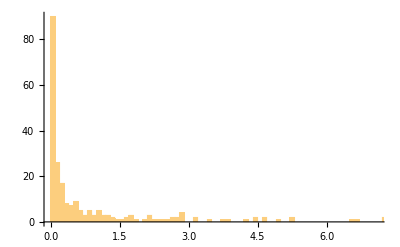

```mathematica
Histogram[-Join@@Transpose[bst][[1]],{0.1}]
```

```mathematica
EstimatedDistribution[-Join@@Transpose[bst][[1]],LogNormalDistribution[μ,σ]]
```

LogNormalDistribution[-1.20942,2.33618]

```mathematica
bcs=Flatten[Outer[List,bs1,cs,1],1];
```

```mathematica
bcs=bst;
```

```mathematica
mm1=Outer[((matrixel1[#1,#2,1.5]+matrixel1[#1,p121[#2],1.5])/Sqrt[(1.+ovlel1[#2,p121[#2]])(1.+ovlel1[#1,p121[#1]])])&,bcs,bcs,1];
```

```mathematica
ov1=Map[#[[1]]&,mm1,{2}];
```

```mathematica
Take[ArrayRules[SparseArray[Chop[ov1-Transpose[ov1]]]],10]
```

Take::take: Cannot take positions 1 through 10 in {{_,_}→0}.

Take[{{_,_}→0},10]

```mathematica
Eigenvalues[ov1]
```

{29.1289,19.2222,13.279,11.4258,9.00228,7.03241,5.73148,5.42038,5.04993,4.61651,3.56353,3.2766,2.96298,2.89648,2.42018,2.31798,1.98589,1.80725,1.5725,1.53422,1.49409,1.33848,1.30851,1.25626,1.19013,1.08654,0.923701,0.893391,0.846395,0.797563,0.76288,0.695071,0.673441,0.650225,0.612228,0.586886,0.514489,0.501641,0.492868,0.461699,0.407309,0.360288,0.345766,0.314574,0.312645,0.301732,0.294599,0.274139,0.258282,0.233989,0.204878,0.195638,0.191645,0.165465,0.156769,0.148613,0.140014,0.135672,0.130293,0.118778,0.115089,0.107876,0.106583,0.0940749,0.0883229,0.0853483,0.0800854,0.0726605,0.0687933,0.0656409,0.0608629,0.0579478,0.0562355,0.0530054,0.048227,0.0465365,0.0426042,0.0373309,0.0368053,0.0356118,0.0330558,0.0317233,0.0303808,0.027266,0.0266943,0.025385,0.0232994,0.0228017,0.0218488,0.0209238,0.0191361,0.0176449,0.017266,0.0167725,0.0150765,0.014736,0.0132476,0.012671,0.0119057,0.0111956,0.0105869,0.0104792,0.00899824,0.00874367,0.00867899,0.00772125,0.00727138,0.00710954,0.00698242,0.00671104,0.00622622,0.00608076,0.00568187,0.00558858,0.00534352,0.00500441,0.00478338,0.00458284,0.00451946,0.00426167,0.00410971,0.00386884,0.00374471,0.00346977,0.00330683,0.00313268,0.00300605,0.00289343,0.00266979,0.0026337,0.00249234,0.00241246,0.0022124,0.00202817,0.00197907,0.00180998,0.00173917,0.00171485,0.00154256,0.00147081,0.00140986,0.00137162,0.00133014,0.00126907,0.000998772,0.000987647,0.000945663,0.000919592,0.000818295,0.000778082,0.000745367,0.000694493,0.00067595,0.000665172,0.000587911,0.000565935,0.000554187,0.000320261}

```mathematica
ham1=Map[#[[2]]&,mm1,{2}];
```

```mathematica
ev1=Sort[Eigenvalues[{ham1,ov1}]]
```

{-0.150253,-0.0675856,0.0448585,0.0613867,0.150947,0.206403,0.23364,0.266544,0.273937,0.35757,0.398035,0.424099,0.462555,0.496753,0.577548,0.64015,0.661339,0.683174,0.731556,0.850264,0.896902,0.965659,1.00161,1.05859,1.14193,1.18282,1.26156,1.29579,1.37814,1.46207,1.6209,1.68317,1.78912,1.91822,2.0093,2.09241,2.28537,2.36258,2.56678,2.73214,2.88235,2.99933,3.02917,3.18233,3.31528,3.38586,3.5929,3.73759,3.9232,3.95807,4.11885,4.1386,4.45598,4.74605,5.00902,5.40548,5.87651,5.92446,6.13186,6.18526,6.51943,6.66761,6.70745,6.94108,7.37788,7.80412,8.13965,8.29204,8.6168,8.75237,9.10078,9.24502,9.68701,10.6766,10.817,11.7435,11.9835,12.4225,12.479,12.9534,13.6962,14.1047,14.4929,14.8399,15.7985,16.3928,16.4367,17.3331,18.0264,18.7435,19.9327,20.5833,20.6683,21.2052,22.1483,23.2964,23.8222,23.9298,24.215,25.7526,27.2296,27.7081,27.9796,29.0846,29.6908,32.6479,33.1485,35.7214,36.762,39.0183,41.546,43.5417,43.9192,44.3425,45.928,47.6193,48.2579,50.5082,51.3432,56.5429,56.7295,58.9706,61.2111,62.5311,65.9992,68.9771,70.491,73.8502,75.6093,76.6862,78.9946,82.084,84.3524,85.1048,90.6907,92.8225,96.3281,105.717,107.096,119.336,126.64,140.587,143.921,150.822,157.069,171.399,183.706,193.68,198.481,218.145,245.666,255.657,295.093,308.884,325.364,444.192,814.109,841.495}

```mathematica
ind=Table[i,{i,Length[ev1]}]-1;
```

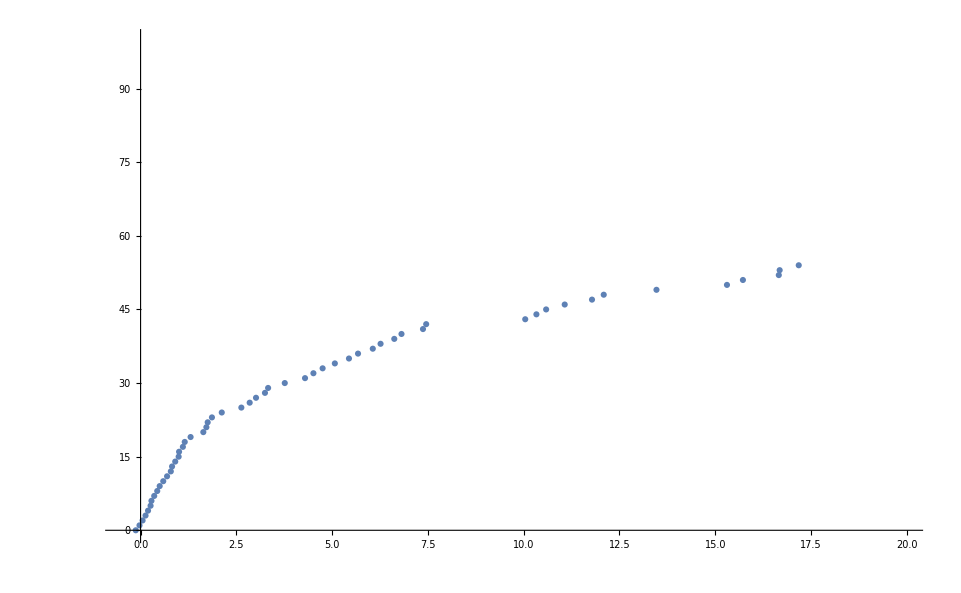

```mathematica
ListPlot[Transpose[{ev1,ind}],PlotRange->{{-0.5,20},{-0.5,100}},PlotMarkers->Automatic]
```

```mathematica
ov1=(ov1+Transpose[ov1])/2;ham1=(ham1+Transpose[ham1])/2;
```

```mathematica
sel[min_:0]:=Block[{mt=Eigensystem[ov1],evl,trf,dg}, {evl,trf}=Transpose[Select[Transpose[mt],#[[1]]>min&]];dg=DiagonalMatrix[1/Sqrt[evl]];Sort[Eigenvalues[dg.trf.ham1.Transpose[trf].dg]]]
```

```mathematica
sel[10^-4]
```

{-0.126167,-0.0283347,0.0526435,0.129582,0.194625,0.261141,0.284007,0.355782,0.434644,0.498977,0.591749,0.691513,0.789211,0.821735,0.904406,0.99376,1.0049,1.1043,1.15261,1.30553,1.63771,1.71744,1.75171,1.86268,2.11902,2.63032,2.84767,3.01295,3.24648,3.32871,3.76355,4.29212,4.51131,4.75138,5.07048,5.4393,5.67545,6.06082,6.26387,6.62157,6.80998,7.37093,7.45424,10.0395,10.3314,10.5851,11.0701,11.7823,12.0887,13.4651,15.3051,15.7213,16.6579,16.6803,17.1783,20.9058,21.1624,21.449,23.2602,23.8112,25.3484,26.651,30.7374,32.9173,40.2087,40.8393,44.8346,46.3367,47.9314,54.2186,59.1693,65.5999,66.7337,67.9768,75.0681,88.5805,93.3533,93.7991,124.689,142.211,159.451,206.424,289.577,771.457}

```mathematica
sel[min_:0]:=Block[{mt=Eigensystem[ov1],evl,trf,dg,es,evs}, {evl,trf}=Transpose[Select[Transpose[mt],#[[1]]>min&]];dg=DiagonalMatrix[1/Sqrt[evl]];{es,evs}=Eigensystem[dg.trf.ham1.Transpose[trf].dg];{es,Transpose[trf].dg.evs}]
```

```mathematica
{ess,evss}=sel[0.1];
```

## LIT

```mathematica
Clear[ovl];ovl[bc_,bp_,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,cp,cm,cpp,cpm,ovl,ovl0,kin,pot, s,λ0=1.4,v2},
bs=bc[[1]]+bp;
{α,β,γ}=αβγ[bc[[1]]];{αp,βp,γp}=αβγ[bp]; {αs,βs,γs}=αβγ[bs];
{cp,cm}=ctopm[bc[[2]]];{cpp,cpm}={2/3,0};

ovl0=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)/(dαβγc[2α,2β,2γ,cm cm,cp cp,2cm cp]^(1/2));
ovl0
dαβγc[α+αp,β+βp,γ+γp,cm cpm,cp cpp,cpm cp+cm cpp]
]
```

```mathematica
ovmat=Outer[(ovl[#1,#2]+ovl[#1,p12[#2]])/Sqrt[(1.+ovlel1[#1,p121[#1]])(1.+ovlel[#2,p12[#2]])]&,bcs,bs,1];
```

```mathematica
rhs=ovmat.gs
```

{-0.362831,0.0795175,0.0973447,0.0540076,0.355672,-0.216112,0.310061,0.221043,0.611064,0.0361656,-0.197939,0.0253157,0.0635911,0.127643,-0.242467,0.531345,0.357215,-0.261753,0.0125479,-0.0932346,0.0739025,0.195168,-0.0215936,0.245109,0.529689,-0.222311,-0.136229,-0.0190779,0.157121,0.0693448,0.59414,-0.00612456,0.0174865,0.0265779,0.306576,0.193005,0.533362,0.0828699,0.283776,0.0413049,0.356424,0.0239891,0.0286174,0.331953,0.293563,0.374915,0.0906539,0.113949,0.0187083,0.60061,-0.0705307,0.0475805,0.184753,-0.186662,0.139756,-0.0053475,0.693234,-0.32248,0.507796,0.00498838,0.331634,0.388086,-0.1674,0.0370331,-0.113678,-0.148518,-0.0116019,0.406656,-0.327621,-0.243465,0.247497,0.0779678,0.67083,-0.0462685,0.144928,0.412402,0.0700744,-0.138989,-0.328357,-0.233432,-0.127438,0.382678,0.277955,-0.106498,0.64721,0.0963089,0.390067,0.374202,0.0224755,0.0205829,-0.0448615,0.161301,0.154627,0.232045,0.0541439,0.0120417,0.176103,-0.0168306,0.0356484,-0.0095963,0.263996,0.0019097,-0.0185083,-0.125717,0.0094673,0.370847,0.347806,0.0569899,0.135405,0.112754,0.29633,0.0242001,0.00156296,-0.0430552,-0.0504992,-0.261019,0.0321856,0.567442,0.0414216,0.174716,0.152239,-0.203597,0.00439293,0.114118,-0.0300279,0.369397,0.20113,0.702987,0.250446,0.235228,0.0515736,0.00924349,-0.148664,0.0679305,0.0910179,0.453683,0.0295005,0.21489,0.0208792,-0.0961331,0.052945,0.311261,-0.0102438,0.0943702,0.247253,0.125536,0.0578128,0.0398254,0.171581,0.19036,-0.304871,0.671525,0.0764652,-0.321505,0.309418,0.454649,-0.0679268,-0.121101}

```mathematica
es=Eigensystem[{ham1,ov1}];
```

```mathematica
evs=Table[es[[2,i]]/Sqrt[es[[2,i]].ov1.es[[2,i]]],{i,Length[es[[1]]]}];
```

```mathematica
Length[evs[[1]]]
```

158

```mathematica
Sort[Transpose[es],#⟦1⟧<#2⟦1⟧&][[;;2]];
```

```mathematica
Sort[Transpose[{es[[1]],(#.rhs)^2&/@evs}],#⟦1⟧<#2⟦1⟧&];
```

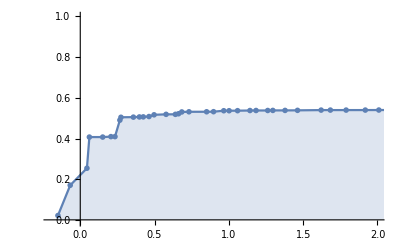

```mathematica
sm=0;ListLinePlot[{#[[1]],sm+=#[[2]]}&/@Sort[Transpose[{es[[1]],(#.rhs)^2&/@evs}],#⟦1⟧<#2⟦1⟧&],PlotMarkers->"OpenMarkers",Filling->Axis,PlotRange->{{-0.2,2},{-0.01,1}}]
```

```mathematica
sm
```

0.540357

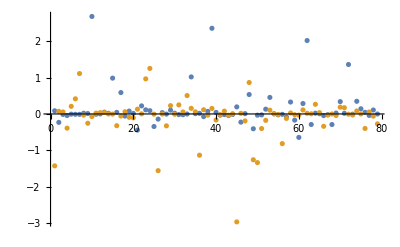

```mathematica
ListPlot[{evs[[1,;;;;2]],evs[[5,2;;;;2]]},PlotRange->All]
```

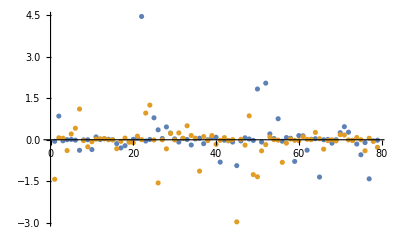

```mathematica
ListPlot[{evs[[5,;;;;2]],evs[[5,2;;;;2]]},PlotRange->All]
```

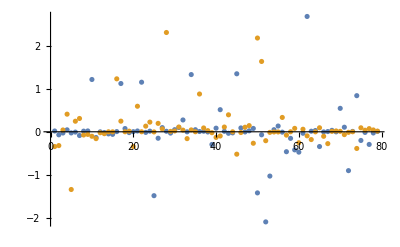

```mathematica
ListPlot[{evs[[6,;;;;2]],evs[[6,2;;;;2]]},PlotRange->All]
```

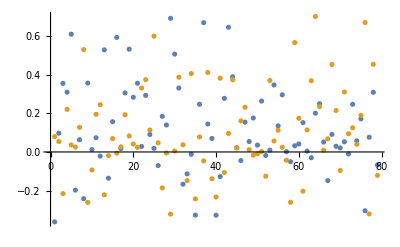

```mathematica
ListPlot[{rhs[[;;;;2]],rhs[[2;;;;2]]},PlotRange->All]
```

```mathematica
Table[1/(evs[[i]].evs[[i]]),{i,100}]
```

{0.0223556,0.0488873,0.0337868,0.0095326,0.0161204,0.0212162,0.00942231,0.00630506,0.00681173,0.00353804,0.00990184,0.011131,0.00419212,0.00342933,0.00743929,0.00284711,0.0053113,0.00577266,0.00654729,0.00458613,0.00197253,0.0083927,0.00356764,0.00373528,0.00235036,0.00638715,0.00204662,0.0146921,0.00283784,0.0042722,0.00279704,0.00406568,0.00253379,0.00766641,0.00426396,0.0028915,0.00635211,0.00537041,0.0066807,0.003327,0.00290373,0.00681166,0.00480028,0.00325734,0.00264803,0.00519641,0.0049877,0.00508712,0.00765694,0.0064118,0.00378381,0.00443751,0.0050675,0.00168582,0.00303606,0.00472328,0.00387055,0.00244442,0.00466417,0.00320251,0.00348773,0.00434279,0.00331557,0.00236161,0.00381859,0.00162804,0.00211173,0.00340878,0.00334905,0.00427397,0.00582276,0.00634491,0.0064164,0.00355182,0.00390568,0.00229428,0.00360765,0.00179568,0.00374125,0.00310796,0.00630237,0.00828462,0.00528473,0.00504474,0.00655926,0.00303245,0.00374011,0.00319861,0.0028297,0.00346867,0.00617256,0.00589812,0.00355054,0.0051914,0.00416425,0.00363484,0.00538241,0.0034956,0.00432881,0.0177323}

```mathematica
1/(evs[[6]].evs[[6]])
```

0.0212162

```mathematica
bcs[[1,;;;;2]]
```

{{-0.992058,-0.0471642,-0.141272}}